```mathematica
(* Solve[{x^2+y^2==y*sin(t)+x*cos(t),x^2+y^2==y*sin((3*t)/2)+x*cos((3*t)/2)},{x,y},Reals] *)

(* Solve x *)
Print[FullSimplify[(cos(t) (sin((3 t)/2))^2+(−sin(t) cos((3 t)/2)−cos(t) sin(t)) sin((3 t)/2)+(sin(t))^2 cos((3 t)/2))/((sin((3 t)/2))^2−2 sin(t) sin((3 t)/2)+(cos((3 t)/2))^2−2 cos(t) cos((3 t)/2)+(sin(t))^2+(cos(t))^2)]];
Print[TrigExpand[(Cos[t]+Cos[3t/2])/2]];
Print[FullSimplify[2 Cos[t/2]^3+Cos[t/2]^2-3/2 Cos[t/2]-1/2 ]];
```

1/2 (Cos[t]+Cos[(3 t)/2])

1/2 Cos[t/2]^2+1/2 Cos[t/2]^3-1/2 Sin[t/2]^2-3/2 Cos[t/2] Sin[t/2]^2

1/2 (Cos[t]+Cos[(3 t)/2])

```mathematica
(* Solve y *)
Print[FullSimplify[−((cos(t) cos((3 t)/2)−(cos(t))^2) sin((3 t)/2)−sin(t) (cos((3 t)/2))^2+cos(t) sin(t) cos((3 t)/2))/((sin((3 t)/2))^2−2 sin(t) sin((3 t)/2)+(cos((3 t)/2))^2−2 cos(t) cos((3 t)/2)+(sin(t))^2+(cos(t))^2)]];
Print[TrigExpand[(Sin[t]+Sin[3t/2])/2]];
Print[FullSimplify[2Sin[t/2] Cos[t/2]^2+Sin[t/2]Cos[t/2]-1/2 Sin[t/2] ]];
```

1/2 (Sin[t]+Sin[(3 t)/2])

Cos[t/2] Sin[t/2]+3/2 Cos[t/2]^2 Sin[t/2]-1/2 Sin[t/2]^3

1/2 (Sin[t]+Sin[(3 t)/2])

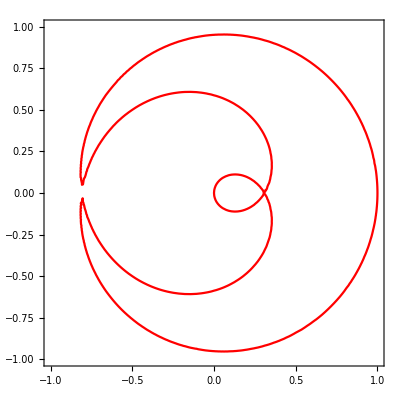

```mathematica
ContourPlot[0==16 y^6+48 x^2 y^4−20 y^4+48 x^4 y^2−40 x^2 y^2+5 y^2+16 x^6−20 x^4+5 x^2−x,{x,-1,1},{y,-1,1}, ContourStyle->Red]
```

Now we evolve the Blue Curve Piece.
First the we solve for x and then for y.

```mathematica
(* Solve[{x^2+y^2==y*sin(t)+x*cos(t),x^2+y^2==-y*sin((3*t)/4)-x*cos((3*t)/4)},{x,y},Reals] *)

(* Solve x *)
Print[FullSimplify[−((cos((3 t)/4) (sin(t))^2+(cos((3 t)/4) sin((3 t)/4)−sin((3 t)/4) cos(t)) sin(t)−(sin((3 t)/4))^2 cos(t))/((sin(t))^2+2 sin((3 t)/4) sin(t)+(cos(t))^2+2 cos((3 t)/4) cos(t)+(sin((3 t)/4))^2+(cos((3 t)/4))^2))]];
Print[TrigExpand[(Cos[t]-Cos[3t/4])/2]];
Print[FullSimplify[4 Cos[t/4]^4-2 Cos[t/4]^3-4 Cos[t/4]^2+3/2 Cos[t/4]+1/2 ]];
```

1/2 (-Cos[(3 t)/4]+Cos[t])

-1/2 Cos[t/4]^3+1/2 Cos[t/4]^4+3/2 Cos[t/4] Sin[t/4]^2-3 Cos[t/4]^2 Sin[t/4]^2+1/2 Sin[t/4]^4

1/2 (-Cos[(3 t)/4]+Cos[t])

```mathematica
(* Solve y *)
Print[FullSimplify[((cos((3 t)/4) cos(t)+(cos((3 t)/4))^2) sin(t)−sin((3 t)/4) (cos(t))^2−cos((3 t)/4) sin((3 t)/4) cos(t))/((sin(t))^2+2 sin((3 t)/4) sin(t)+(cos(t))^2+2 cos((3 t)/4) cos(t)+(sin((3 t)/4))^2+(cos((3 t)/4))^2)]];
Print[TrigExpand[(Sin[t]-Sin[3t/4])/2]];
Print[FullSimplify[4Sin[t/4] Cos[t/4]^3-2Sin[t/4] Cos[t/4]^2-2Sin[t/4]Cos[t/4]+1/2 Sin[t/4] ]];
```

1/2 (-Sin[(3 t)/4]+Sin[t])

-3/2 Cos[t/4]^2 Sin[t/4]+2 Cos[t/4]^3 Sin[t/4]+1/2 Sin[t/4]^3-2 Cos[t/4] Sin[t/4]^3

1/2 (-Sin[(3 t)/4]+Sin[t])

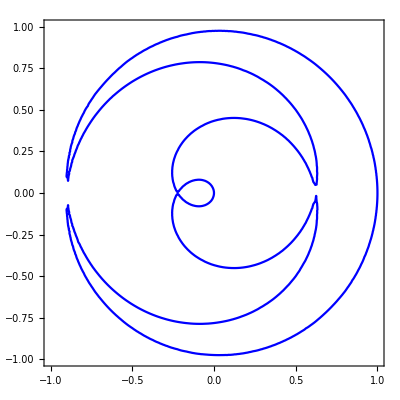

```mathematica
ContourPlot[0==-64*y^8-256*x^2*y^6+112*y^6-384*x^4*y^4+336*x^2*y^4-56*y^4-256*x^6*y^2+336*x^4*y^2-112*x^2*y^2+7*y^2-64*x^8+112*x^6-56*x^4+7*x^2+x,{x,-1,1},{y,-1,1},ContourStyle->Blue]
```

Let us put both curves in one chart
The red curve piece and the blue curve piece.

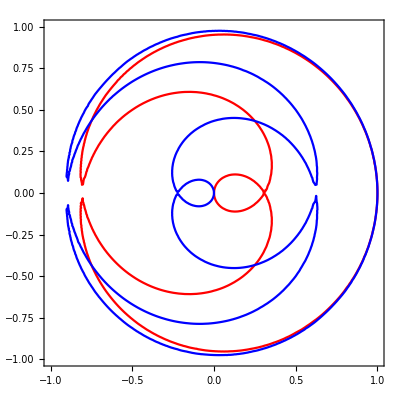

```mathematica
plot1=ContourPlot[0==16 y^6+48 x^2 y^4−20 y^4+48 x^4 y^2−40 x^2 y^2+5 y^2+16 x^6−20 x^4+5 x^2−x,{x,-1,1},{y,-1,1}, ContourStyle->Red];
plot2=ContourPlot[0==-64*y^8-256*x^2*y^6+112*y^6-384*x^4*y^4+336*x^2*y^4-56*y^4-256*x^6*y^2+336*x^4*y^2-112*x^2*y^2+7*y^2-64*x^8+112*x^6-56*x^4+7*x^2+x,{x,-1,1},{y,-1,1},ContourStyle->Blue];
Show[plot1,plot2]
```